# Plotting solutions to the Kerr Metric

### Introduction

This notebook closely follows a previously developed Mathematica notebook on Kerr solutions, developed by Erik Tollerud and found on his personal website here: https://www.physics.uci.edu/~etolleru/KerrOrbitProject.pdf

The authors of this notebook have followed the above resource and reproduced the results to build some more intuition for what happens to orbits near rotating black holes.

### Creating the Schwarzschild metric

Following the derivations in our PRL article, we can construct the kerr metric as follows and show the matrix representation of the metric

```mathematica
coords = {t,r,θ,ϕ}
n=Length[coords];
tt=2 M r/ρ-1;
rr=ρ/Δ;
θθ=ρ;
ϕϕ=(Δ+(2 M r (r^2+a^2))/ρ)Sin[θ]^2;
tϕ=-4 a M r Sin[θ]^2/ρ;
metric={{tt,0,0,tϕ},{0,rr,0,0},{0,0,θθ,0},{tϕ,0,0,ϕϕ}};
metric//MatrixForm
inversemetric=Simplify[Inverse[metric]];
inversemetric //MatrixForm
```

{t,r,θ,ϕ}

(-1+(2 M r)/ρ | 0 | 0 | -(4 a M r Sin[θ]^2)/ρ
0 | ρ/Δ | 0 | 0
0 | 0 | ρ | 0
-(4 a M r Sin[θ]^2)/ρ | 0 | 0 | (Δ+(2 M r (a^2+r^2))/ρ) Sin[θ]^2)

(-(ρ (2 a^2 M r+2 M r^3+Δ ρ))/(2 a^2 M r (2 M r+ρ)-(2 M r-ρ) (2 M r^3+Δ ρ)-8 a^2 M^2 r^2 Cos[2 θ]) | 0 | 0 | (4 a M r ρ)/(-2 a^2 M r (2 M r+ρ)+(2 M r-ρ) (2 M r^3+Δ ρ)+8 a^2 M^2 r^2 Cos[2 θ])
0 | Δ/ρ | 0 | 0
0 | 0 | 1/ρ | 0
(4 a M r ρ)/(-2 a^2 M r (2 M r+ρ)+(2 M r-ρ) (2 M r^3+Δ ρ)+8 a^2 M^2 r^2 Cos[2 θ]) | 0 | 0 | -(ρ (-2 M r+ρ) Csc[θ]^2)/(-2 a^2 M r (2 M r+ρ)+(2 M r-ρ) (2 M r^3+Δ ρ)+8 a^2 M^2 r^2 Cos[2 θ]))

By setting a=0, i.e. no angular momentum (recall that a=J/M), we recover the metric of a more normal Schwarzschild black hole, with all diagonal terms.

```mathematica
a=0;
ρ=r^2+a^2 Cos[θ]^2;
Δ=r^2 - 2 M r+ a^2;
metric//MatrixForm
```

(-1+(2 M)/r | 0 | 0 | 0
0 | r^2/(-2 M r+r^2) | 0 | 0
0 | 0 | r^2 | 0
0 | 0 | 0 | r^2 Sin[θ]^2)

### Calculating Christoffel symbols in the Schwarzschild Metric

Mathematica is great at doing all the heavy lifting for us in calculating christoffel symbols. This calculation borrowed heavily from the following resource: http://web.physics.ucsb.edu/~gravitybook/math/christoffel.pdf, and Erik Tollerud’s work.

```mathematica
christoffel:=christoffel=Simplify[Table[(1/2)*Sum[(inversemetric[[i,s]])*
(D[metric[[s,j]],coords[[k]] ]+
D[metric[[s,k]],coords[[j]] ]-D[metric[[j,k]],coords[[s]] ]),{s,1,n}],
{i,1,n},{j,1,n},{k,1,n}] ]
listchristoffel:=Table[If[UnsameQ[christoffel[[i,j,k]],0],{ToString[Γ[i,j,k]],christoffel[[i,j,k]]}] ,{i,1,n},{j,1,n},{k,1,j}]
TableForm[Partition[DeleteCases[Flatten[listchristoffel],Null],2],TableSpacing->{2,2}]
```

Γ[1, 2, 1] | -M/(2 M r-r^2)
Γ[2, 1, 1] | (M (-2 M+r))/r^3
Γ[2, 2, 2] | M/(2 M r-r^2)
Γ[2, 3, 3] | 2 M-r
Γ[2, 4, 4] | (2 M-r) Sin[θ]^2
Γ[3, 3, 2] | 1/r
Γ[3, 4, 4] | -Cos[θ] Sin[θ]
Γ[4, 4, 2] | 1/r
Γ[4, 4, 3] | Cot[θ]

We can also calculate the geodesic differential equations as we’ve done in the course of lecture multiple times. Solutions to these differential equations correspond to geodesics in the metric.

```mathematica
geodesic:=geodesic=Simplify[Table[-Sum[christoffel[[i,j,k]]coords[[j]]' coords[[k]]',{j,1,n},
{k,1,n}],{i,1,n}]]
listgeodesic:=Table[{"d/dτ"ToString[coords[[i]]'],"=",geodesic[[i]]},{i,1,n}]
TableForm[listgeodesic,TableSpacing->{2}]
```

d/dτ t' | = | (2 M r' t')/(2 M r-r^2)
d/dτ r' | = | (-M r^2 (r')^2+(-2 M+r)^2 (M (t')^2-r^3 ((θ')^2+Sin[θ]^2 (ϕ')^2)))/((2 M-r) r^3)
d/dτ θ' | = | -(2 r' θ')/r+Cos[θ] Sin[θ] (ϕ')^2
d/dτ ϕ' | = | -(2 (r'+r Cot[θ] θ') ϕ')/r

Now we can use Mathematica’s NDSolve to solve this system of differential equations for the trajectories of the orbits. This solver and conversion to euclidean coordinates were not written by the authors but are credited to Erik Tollerud.

```mathematica
computeSoln[maxτi_,ivsi_,icsi_]:=Block[{ivs,ics,i,χ,tmp,soln},
ics=icsi;
ivs=Join[{χ},ivsi];
tmp=metric;
tmp=tmp/.Table[coords[[i]]->ics[[i]],{i,0,n}];
tmp=ivs.(tmp.ivs);
χslv=Solve[tmp==uinvar,χ];
ivs[[1]]=Last[χ/.χslv];
deq=Table[coords[[i]]''[τ]==(geodesic[[i]]/.Join[Table[coords[[i]]'->coords[[i]]'[τ],{i,1,n}],Table[coords[[i]]->coords[[i]][τ],{i,1,n}]]),{i,1,n}];
deq=Join[deq,Table[coords[[i]]'[0]==ivs[[i]],{i,1,n}],Table[coords[[i]][0]==ics[[i]],{i,1,n}]];
soln=NDSolve[deq,coords,{τ,0,maxτi}];
soln]
uinvar=-1;
sphslnToCartsln[soln_]:=Block[{xs,ys,zs},xs=r[τ] Sin[θ[τ]] Cos[ϕ[τ]]/.soln ;ys=r[τ] Sin[θ[τ]] Sin[ϕ[τ]]/.soln;zs=r[τ] Cos[θ[τ]]/.soln;{xs,ys,zs}]
udotu[solni_,τval_]:=Block[{xα,uα},xα=Table[coords[[i]][τ]/.solni,{i,1,n}]//Flatten; uα=D[xα,τ];
xα=xα/.τ->τval;uα=uα/.τ->τval;uα.((metric/.Table[coords[[i]]->xα[[i]],{i,1,n}]).uα)]
coordlist[τin_]:=Table[ToString[coords[[i]]]<>" = "<>{ToString[coords[[i]][τin]/.soln//First]},{i,1,n}]
```

### Schwarszchild Orbits

Here we use the solver and S-metric to find orbits for the non-rotating black hole, with orbit in blue and event horizon in red.

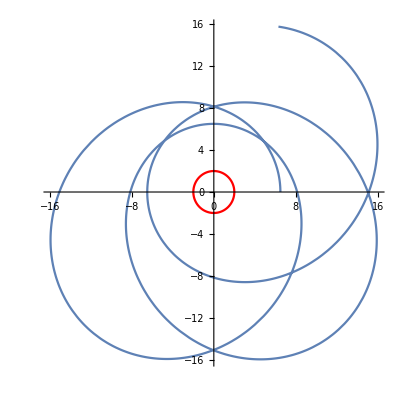

```mathematica
maxτ=750;
ivs={0,0,.088};
ics={0,6.5,π/2,0};
M=1;
soln=computeSoln[maxτ,ivs,ics];
Plot[Evaluate[Table[coords[[i]][τ]/.soln,{i,1,n}]],{τ,0,maxτ},PlotStyle->Table[Hue[(i-1)/n],{i,1,n}],PlotLegends->coords,AxesLabel->{"τ","Coordinate"}];
xyzsoln=sphslnToCartsln[soln];
horizpl=PolarPlot[2,{θ,0,2 Pi},PlotStyle->Hue[0],DisplayFunction->Identity];
ParametricPlot[Evaluate[{xyzsoln[[1]],xyzsoln[[2]]}//Flatten],{τ,0,maxτ},AspectRatio->1,DisplayFunction->Identity];
Show[%,horizpl,DisplayFunction->$DisplayFunction]
```

### Rotating black hole - Kerr metric

Now we go for the fully general Kerr Solution for when the orbits do not strictly lie in a plane. The Christoffel symbols become quite a mess but Mathematica takes care of it for us nicely.

```mathematica
a=.;M=.;
ρ=r^2+a^2 Cos[θ]^2;
Δ=r^2 - 2 M r+ a^2;
christoffel:=christoffel=Simplify[Table[(1/2)*Sum[(inversemetric[[i,s]])*
(D[metric[[s,j]],coords[[k]] ]+
D[metric[[s,k]],coords[[j]] ]-D[metric[[j,k]],coords[[s]] ]),{s,1,n}],
{i,1,n},{j,1,n},{k,1,n}] ]
TableForm[Partition[DeleteCases[Flatten[listchristoffel],Null],2],TableSpacing->{2,2}]
geodesic:=geodesic=Simplify[Table[-Sum[christoffel[[i,j,k]]coords[[j]]' coords[[k]]',{j,1,n},
{k,1,n}],{i,1,n}]]
TableForm[Partition[DeleteCases[Flatten[listgeodesic],Null],2],TableSpacing->{2,2}]
```

Γ[1, 2, 1] | -(M (a^2-2 r^2+a^2 Cos[2 θ]) (a^4+2 r^4+3 a^2 r (-2 M+r)+a^2 (a^2+r (6 M+r)) Cos[2 θ]))/(4 (r^2+a^2 Cos[θ]^2) (2 a^2 r^2 (a^2+2 M^2-2 M r+r^2) Cos[θ]^2+a^4 (a^2+r (-2 M+r)) Cos[θ]^4+r^2 (r^3 (-2 M+r)+a^2 (4 M^2+r^2)-8 a^2 M^2 Cos[2 θ])))
Γ[1, 3, 1] | -(a^2 M r Cos[θ] (a^4+2 r^3 (-8 M+r)+a^2 r (-14 M+3 r)+a^2 (a^2+r (-2 M+r)) Cos[2 θ]) Sin[θ])/((r^2+a^2 Cos[θ]^2) (2 a^2 r^2 (a^2+2 M^2-2 M r+r^2) Cos[θ]^2+a^4 (a^2+r (-2 M+r)) Cos[θ]^4+r^2 (r^3 (-2 M+r)+a^2 (4 M^2+r^2)-8 a^2 M^2 Cos[2 θ])))
Γ[1, 4, 2] | (2 a M (-r^2 (a^2+3 r^2)+a^2 (a^2-r^2) Cos[θ]^2) Sin[θ]^2)/(2 a^2 r^2 (a^2+2 M^2-2 M r+r^2) Cos[θ]^2+a^4 (a^2+r (-2 M+r)) Cos[θ]^4+r^2 (r^3 (-2 M+r)+a^2 (4 M^2+r^2)-8 a^2 M^2 Cos[2 θ]))
Γ[1, 4, 3] | (4 a^3 M r (a^2+r (-2 M+r)) Cos[θ] Sin[θ]^3)/(2 a^2 r^2 (a^2+2 M^2-2 M r+r^2) Cos[θ]^2+a^4 (a^2+r (-2 M+r)) Cos[θ]^4+r^2 (r^3 (-2 M+r)+a^2 (4 M^2+r^2)-8 a^2 M^2 Cos[2 θ]))
Γ[2, 1, 1] | -(M (a^2+r (-2 M+r)) (-r^2+a^2 Cos[θ]^2))/((r^2+a^2 Cos[θ]^2)^3)
Γ[2, 2, 2] | (r (a^2-M r)+a^2 (M-r) Cos[θ]^2)/((a^2+r (-2 M+r)) (r^2+a^2 Cos[θ]^2))
Γ[2, 3, 2] | -(a^2 Cos[θ] Sin[θ])/(r^2+a^2 Cos[θ]^2)
Γ[2, 3, 3] | -(r (a^2+r (-2 M+r)))/(r^2+a^2 Cos[θ]^2)
Γ[2, 4, 1] | (2 a M (a^2+r (-2 M+r)) (-r^2+a^2 Cos[θ]^2) Sin[θ]^2)/((r^2+a^2 Cos[θ]^2)^3)
Γ[2, 4, 4] | ((a^2+r (-2 M+r)) (a^2 M r^2-r^5-a^2 (a^2 M+r^2 (M+2 r)) Cos[θ]^2+a^4 (M-r) Cos[θ]^4) Sin[θ]^2)/((r^2+a^2 Cos[θ]^2)^3)
Γ[3, 1, 1] | -(2 a^2 M r Cos[θ] Sin[θ])/((r^2+a^2 Cos[θ]^2)^3)
Γ[3, 2, 2] | (a^2 Cos[θ] Sin[θ])/((a^2+r (-2 M+r)) (r^2+a^2 Cos[θ]^2))
Γ[3, 3, 2] | r/(r^2+a^2 Cos[θ]^2)
Γ[3, 3, 3] | -(a^2 Cos[θ] Sin[θ])/(r^2+a^2 Cos[θ]^2)
Γ[3, 4, 1] | (2 a M r (a^2+r^2) Sin[2 θ])/((r^2+a^2 Cos[θ]^2)^3)
Γ[3, 4, 4] | (Cos[θ] Sin[θ] (-(r^2+a^2 Cos[θ]^2)^2 (a^2-2 M r+r^2+(2 M r (a^2+r^2))/(r^2+a^2 Cos[θ]^2))-2 a^2 M r (a^2+r^2) Sin[θ]^2))/((r^2+a^2 Cos[θ]^2)^3)
Γ[4, 2, 1] | (2 a M (r^2-a^2 Cos[θ]^2))/(2 a^2 r^2 (a^2+2 M^2-2 M r+r^2) Cos[θ]^2+a^4 (a^2+r (-2 M+r)) Cos[θ]^4+r^2 (r^3 (-2 M+r)+a^2 (4 M^2+r^2)-8 a^2 M^2 Cos[2 θ]))
Γ[4, 3, 1] | -(4 a M r (a^2+r (-2 M+r)) Cot[θ])/(2 a^2 r^2 (a^2+2 M^2-2 M r+r^2) Cos[θ]^2+a^4 (a^2+r (-2 M+r)) Cos[θ]^4+r^2 (r^3 (-2 M+r)+a^2 (4 M^2+r^2)-8 a^2 M^2 Cos[2 θ]))
Γ[4, 4, 2] | (2 a^2 M^2 r^3-a^2 M r^4-2 M r^6+r^7-a^2 r (2 a^2 M^2+r^2 (2 M^2+3 M r-3 r^2)) Cos[θ]^2+a^4 (a^2 M+r (2 M^2-2 M r+3 r^2)) Cos[θ]^4-a^6 (M-r) Cos[θ]^6-8 a^2 M^2 r^3 Sin[θ]^2+2 a^4 M^2 r Sin[2 θ]^2)/((r^2+a^2 Cos[θ]^2) (2 a^2 r^2 (a^2+2 M^2-2 M r+r^2) Cos[θ]^2+a^4 (a^2+r (-2 M+r)) Cos[θ]^4+r^2 (r^3 (-2 M+r)+a^2 (4 M^2+r^2)-8 a^2 M^2 Cos[2 θ])))
Γ[4, 4, 3] | (Cot[θ] (a^4 r^2 (3 a^2+4 M^2-6 M r+3 r^2) Cos[θ]^4+a^6 (a^2+r (-2 M+r)) Cos[θ]^6+r^2 (r^5 (-2 M+r)+a^4 M (6 M+r)+a^2 r^2 (2 M^2+M r+r^2)-a^2 M (6 M+r) (a^2+r^2) Cos[2 θ])+a^2 r Cos[θ]^2 (r^3 (4 M^2-6 M r+3 r^2)+a^2 (-4 M^2 r+3 r^3)+2 a^2 M (a^2+r^2) Sin[θ]^2)))/((r^2+a^2 Cos[θ]^2) (2 a^2 r^2 (a^2+2 M^2-2 M r+r^2) Cos[θ]^2+a^4 (a^2+r (-2 M+r)) Cos[θ]^4+r^2 (r^3 (-2 M+r)+a^2 (4 M^2+r^2)-8 a^2 M^2 Cos[2 θ])))

d/dτ t' | =
(M (a^2 r θ' (2 (a^4+2 r^3 (-8 M+r)+a^2 r (-14 M+3 r)+a^2 (a^2+r (-2 M+r)) Cos[2 θ]) Sin[2 θ] t'-8 a (a^2+r (-2 M+r)) Cos[θ] (a^2+2 r^2+a^2 Cos[2 θ]) Sin[θ]^3 ϕ')+r' ((a^2-2 r^2+a^2 Cos[2 θ]) (a^4+2 r^4+3 a^2 r (-2 M+r)+a^2 (a^2+r (6 M+r)) Cos[2 θ]) t'+8 a ((r^4 (a^2+3 r^2)+(-a^6+a^4 r^2) Cos[θ]^4) Sin[θ]^2+a^2 r^4 Sin[2 θ]^2) ϕ')))/(2 (r^2+a^2 Cos[θ]^2) (2 a^2 r^2 (a^2+2 M^2-2 M r+r^2) Cos[θ]^2+a^4 (a^2+r (-2 M+r)) Cos[θ]^4+r^2 (r^3 (-2 M+r)+a^2 (4 M^2+r^2)-8 a^2 M^2 Cos[2 θ]))) | d/dτ r'
= | (-((r^2+a^2 Cos[θ]^2)^2 (r (a^2-M r)+a^2 (M-r) Cos[θ]^2) (r')^2)/(a^2+r (-2 M+r))+M (a^2+r (-2 M+r)) (-r^2+a^2 Cos[θ]^2) (t')^2+2 a^2 Cos[θ] (r^2+a^2 Cos[θ]^2)^2 Sin[θ] r' θ'+r (a^2+r (-2 M+r)) (r^2+a^2 Cos[θ]^2)^2 (θ')^2-4 a M (a^2+r (-2 M+r)) (-r^2+a^2 Cos[θ]^2) Sin[θ]^2 t' ϕ'-(a^2+r (-2 M+r)) (a^2 M r^2-r^5-a^2 (a^2 M+r^2 (M+2 r)) Cos[θ]^2+a^4 (M-r) Cos[θ]^4) Sin[θ]^2 (ϕ')^2)/((r^2+a^2 Cos[θ]^2)^3)
d/dτ θ' | =
(-(a^2 Cos[θ] (r^2+a^2 Cos[θ]^2)^2 Sin[θ] (r')^2)/(a^2+r (-2 M+r))+a^2 M r Sin[2 θ] (t')^2-2 r (r^2+a^2 Cos[θ]^2)^2 r' θ'+a^2 Cos[θ] (r^2+a^2 Cos[θ]^2)^2 Sin[θ] (θ')^2-4 a M r (a^2+r^2) Sin[2 θ] t' ϕ'-Cos[θ] Sin[θ] (-(r^2+a^2 Cos[θ]^2)^2 (a^2-2 M r+r^2+(2 M r (a^2+r^2))/(r^2+a^2 Cos[θ]^2))-2 a^2 M r (a^2+r^2) Sin[θ]^2) (ϕ')^2)/((r^2+a^2 Cos[θ]^2)^3) | d/dτ ϕ'
= | -(2 (θ' (-2 a M r (a^2+r (-2 M+r)) (a^2+2 r^2+a^2 Cos[2 θ]) Cot[θ] t'+((a^2 r^2 (a^2 (-4 M^2+3 r^2)+r^2 (4 M^2-6 M r+3 r^2)) Cos[θ]^2+a^4 r^2 (3 a^2+4 M^2-6 M r+3 r^2) Cos[θ]^4+a^6 (a^2+r (-2 M+r)) Cos[θ]^6+r^2 (r^5 (-2 M+r)+a^4 M (6 M+r)+a^2 r^2 (2 M^2+M r+r^2)-a^2 M (6 M+r) (a^2+r^2) Cos[2 θ])) Cot[θ]+2 a^4 M r (a^2+r^2) Cos[θ]^3 Sin[θ]) ϕ')+r' (2 a M (r^4-a^4 Cos[θ]^4) t'+(2 a^2 M^2 r^3-a^2 M r^4-2 M r^6+r^7-a^2 r (2 a^2 M^2+2 M^2 r^2+3 M r^3-3 r^4) Cos[θ]^2+a^4 (a^2 M+2 M^2 r-2 M r^2+3 r^3) Cos[θ]^4-a^6 (M-r) Cos[θ]^6-8 a^2 M^2 r^3 Sin[θ]^2+2 a^4 M^2 r Sin[2 θ]^2) ϕ')))/((r^2+a^2 Cos[θ]^2) (2 a^2 r^2 (a^2+2 M^2-2 M r+r^2) Cos[θ]^2+a^4 (a^2+r (-2 M+r)) Cos[θ]^4+r^2 (r^3 (-2 M+r)+a^2 (4 M^2+r^2)-8 a^2 M^2 Cos[2 θ])))

### Plotting Geodesics of the Kerr metric

Now we are ready to do a full simulation of a Kerr orbit. We can choose some orbital parameters but the only interesting case handled well by the solver is when a is very close to M, i.e. critical rotation.

-Graphics3D-

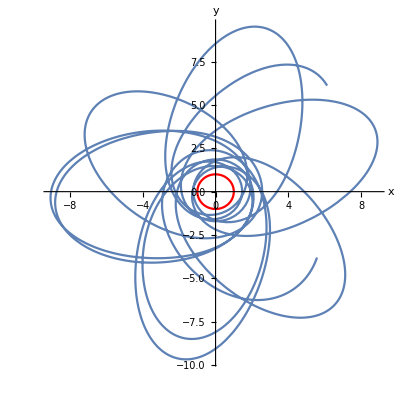

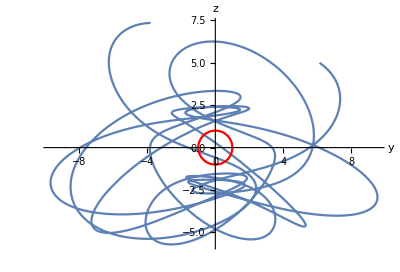

Final Coordinates:
t = 1033.62
r = 9.97908
θ = 0.74225
ϕ = 74.7986

|  |  | u·u values
τ= | 0 | → | -1.
τ= | 160 | → | -1.
τ= | 320 | → | -1.
τ= | 480 | → | -1.
τ= | 640 | → | -1.
τ= | 800 | → | -1.

```mathematica
maxτ=800;M=1;a=1;rplus=M+Sqrt[M^2-a^2];
soln=computeSoln[maxτ,{-0.01,0.01,0.017},{0,10,π/3,Pi/4}];
xyzsoln=sphslnToCartsln[soln];
Plot[Evaluate[Table[coords[[i]][τ]/.soln,{i,1,n}]],{τ,0,maxτ},PlotStyle->Table[Hue[(i-1)/n],{i,1,n}],PlotLegends->coords,AxesLabel->{"τ","Coordinate"}];
SphericalPlot3D[{rplus,EdgeForm[]},{θ,0,Pi},{ϕ,0, 2Pi},DisplayFunction->Identity];
ParametricPlot3D[Evaluate[Re[xyzsoln]//Flatten],{τ,0,maxτ},AxesLabel->{x,y,z},DisplayFunction->Identity,PlotRange->All,PlotPoints->500]


horizpl=PolarPlot[rplus,{θ,0,2 Pi},PlotStyle->Hue[0],DisplayFunction->Identity];
ParametricPlot[Evaluate[Re[{xyzsoln[[1]],xyzsoln[[2]]}]//Flatten],{τ,0,maxτ},AspectRatio->1,AxesLabel->{x,y},DisplayFunction->Identity];
Show[%,horizpl,DisplayFunction->$DisplayFunction]
ParametricPlot[Evaluate[Re[{xyzsoln[[2]],xyzsoln[[3]]}]//Flatten],{τ,0,maxτ},AxesLabel->{y,z},DisplayFunction->Identity];
Show[%,horizpl,DisplayFunction->$DisplayFunction]
ParametricPlot[Evaluate[Re[{xyzsoln[[1]],xyzsoln[[3]]}]//Flatten],{τ,0,maxτ},AxesLabel->{x,z},DisplayFunction->Identity];
Show[%,horizpl,DisplayFunction->$DisplayFunction,AspectRatio->1];
Join[{"Final Coordinates:"},coordlist[maxτ]]//TableForm
Join[{{"","","","u·u values"}},Table[{"τ=",ToString[i],"→",udotu[soln,i]},{i,0,maxτ,maxτ/5}]]//TableForm
```